```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doWarn=False;
doPlot=True;
doSpace=True;
doEPlot=False;

showMistakes=False;
fps=0;

(*Init*)
dir=gFunc@@iterParams;
err=eFunc@@iterParams;

(** Adaptivity **)
errorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)
boostRatio=1.1; (*'Impatience' Multiplier to increase factor when error is not increasing*)
refineRatio=0.95;(*'Caution' Multiplier to decrease factor when error is increasing*)
maxRefines=1000;(*Give up refining if refined too many times in a row*)
(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.01;

(* Tracker values *)
historyAmt=300;

(*Display*)
dispGradientRange=1.;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[q_,samplingRate_,paramVariance_,manualTrueParams_,noiseFactor_, noiseDistribution_,forceData_]:=(
Clear[eFunc,gFunc,params];
ParamVariance=paramVariance;

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
dataLength=Length[Data];
SamplingSet=N[Range[dataLength]]/N[samplingRate];
(* Else *),
SamplingSet=N[Range[dataLength]]/N[samplingRate];
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+noiseFactor*RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];

(*Prep gradient*)
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(* Objective and Gradient functions *)
eFunc=paramh/._[vars__]:>Function[{vars},N[Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];
);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
TotalRefines=0;

(** Modification Values **)
factor=factorx;
dirs=ConstantArray[ConstantArray[0,varamt],Smoothness];
dirX=0;
err=-1;
prevErr=-2;
ConsecRefines=0;

(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};

err=eFunc@@iterParams;
dir=gFunc@@iterParams;
debugErr={err};
);
LinePlot[points_, size_,amount_]:=Show[
ListPointPlot3D[
{If[amount>0&&size>amount,points[[-amount;;-1]],points]},
PlotRange->All,ImageSize->Medium],
Graphics3D@Line@points
];
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
Visualize[]:=Dynamic[Grid[{{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium,PlotLegends->None]
,If[doPoint,If[varamt==3,If[doGraph,
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]},
LinePlot[debugParams,totalIter,historyAmt]],
"Non-3 dimensions"],
"Disabled"],
If[doEPlot,ListLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]
},
{"Parameters, nGrad, dir, Delta","Iterations, factor, corrections"},{Column[{iterParams,-dir,-factor*dir,-factor*SmoothingFunction[dirs]}],Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/maxRefines]}],{(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(dataLength-varamt))^0.5,prevErr}}
},Frame->All,ItemSize->30]];
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[
ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
(* Realtime monitor plot *)
displayGradientNorm[xV_,yV_,ϵ_]:=Show[
ContourPlot[Norm[gFunc @@ ReplacePart[iterParams, {xV->x,yV->y}]],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
RegionFunction->Function[{x,y,z},z≤ϵ], PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
RefineFactor[]:=(factor*=refineRatio^AccelRefine;ConsecRefines++;TotalRefines++;AccelRefine+=AccelAmt;AccelBoost=1.;);
BoostFactor[]:=(factor*=boostRatio^AccelBoost;prevErr=err;ConsecRefines=0;AccelBoost+=AccelAmt;AccelRefine=1.;);
AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];
```

```mathematica
(* SET DATA *)
varamt=3;
dataLength=100;
Fitfunction=#2*Exp[#1*#3]*Sin[#1*#4]&;
InitFunctionData[0,40,3,{},1.,NormalDistribution[],{2.55515,-0.949957,0.954631,0.0679626,0.245159,1.12318,0.699812,1.52914,2.34221,3.58785,3.17743,2.7699,4.71294,6.02167,3.93996,4.08095,6.68862,6.05735,6.25545,6.08665,7.88001,7.24107,6.51588,7.23453,7.40073,9.3045,6.98213,7.66584,9.44697,8.95585,10.8473,11.5192,9.60572,9.18079,8.3529,9.98033,10.4711,10.2755,9.23861,8.09191,7.74405,6.9308,4.91696,2.93346,3.23637,2.7633,2.04864,0.22554,-1.14621,-1.23016,-3.53224,-3.44941,-6.5644,-8.14639,-10.7625,-15.3302,-15.708,-17.414,-22.0694,-24.8501,-25.778,-27.903,-33.6655,-34.5464,-38.3342,-40.446,-42.3715,-48.064,-49.6408,-52.1107,-55.0438,-59.1118,-59.8071,-63.4763,-65.65,-67.7729,-68.3618,-70.1269,-72.7763,-72.818,-73.053,-71.2798,-72.5041,-74.4879,-71.3788,-67.8539,-64.7601,-63.2424,-60.3196,-55.7731,-48.3561,-44.6445,-38.065,-30.4912,-22.268,-12.769,-2.52354,7.4659,18.5826,34.8058}];
```

```mathematica
(* BEGIN ITERATION *)
InitIterationSettings[];
Smoothness=16;
SmoothingFunction[l_]:=Total[MapIndexed[#1 /2.^First[#2]&,l]]/Smoothness;
InitIterationData[0.01,{-2.5,1.5,-2.}];
recordAtIter=200;
Visualize[]
```

```mathematica
(*** Iteration loop ***)

(* Iterator and maximum values *)
i=0.;UpperBound=1000.;
SmallErr=0.0000000000000001;
NoErr=True;
Forever=False;
(* Iteration *)
While[Forever||(i<UpperBound &&(NoErr|| ((err(err-prevErr))^2+1)^2>(1+SmallErr))),
(* Obtain vector from gradient and assign into running array *)
dirs=Prepend[Drop[dirs,-1],dir=gFunc@@iterParams];
ReportIteration[i];(*Report*)If[fps≠0&&ConsecRefines==0,Pause[fps];];(*Pause*)
If[showMistakes,AddToHistory[];];
(*Mark down boost vs error - please do not change other variables*)
iterParams-=factor*SmoothingFunction[dirs];
If[ConsecRefines==0,i++;totalIter++;];
err=eFunc @@ iterParams;
(* Factor Adaptivity - check to see whether error has increased over errorRatio to determine whether to boost or refine *)
If[err/prevErr>errorRatio,
(*If err increased, revert, refine, and retry*)
iterParams=debugParams[[-1]];If[Log10[factor]<-100,factor=0.5];
If[ConsecRefines>maxRefines,If[doWarn,Print["Exceeded maximum amount of consecutive corrections."]];Abort[];,RefineFactor[];];,AddToHistory[];BoostFactor[];];
]
```

```mathematica
(** Data Recording **)
RecordedSmoothnessComparisonData=Catenate[{
RecordedSmoothnessComparisonData,
{{{"Smoothness",Smoothness},debugErr,TotalRefines}}
}];
```

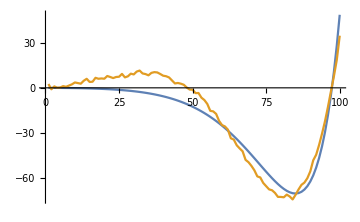

{-2.89082,1.66505,-2.58469}

78.3796

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
(*(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,*)
(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,
Data},Joined->True,ImageSize->Medium]
```

1.5

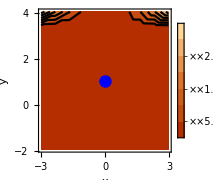
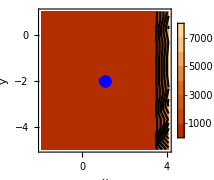
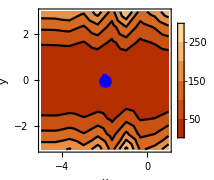

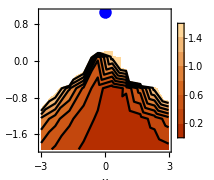
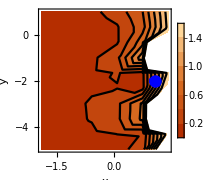
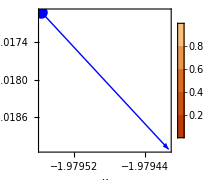

```mathematica
dispGradientRange=3.;
dispGradientThresh=1.5
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]}
{displayGradientNorm[1,2,dispGradientThresh],displayGradientNorm[2,3,dispGradientThresh],displayGradientNorm[3,1,dispGradientThresh]}
```

```mathematica
LinePlot[debugParams,Length[debugParams],100]
```

-Graphics3D-

{1011.47,1.95321,289.878,1.58653,1.03982,1.05195,1.06751,1.07552,1.08353}

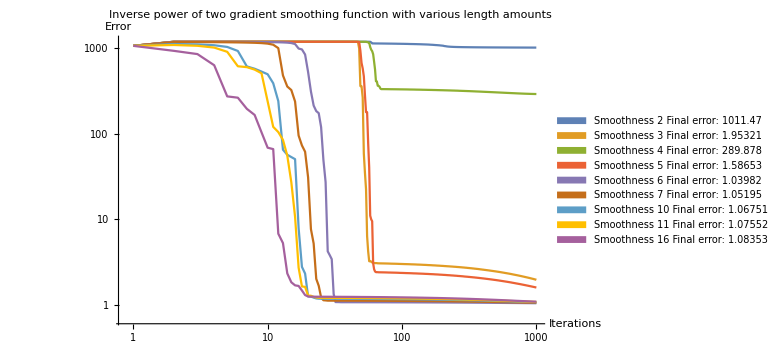

```mathematica
Last/@Table[RecordedSmoothnessComparisonData[[sm,2]],{sm,1,Length@RecordedSmoothnessComparisonData}]
(ListLogLogPlot[
Table[RecordedSmoothnessComparisonData[[sm,2]],{sm,1,Length@RecordedSmoothnessComparisonData}],PlotLegends->SwatchLegend[
Table[
Column[{
ToSpacedString@RecordedSmoothnessComparisonData[[sm,1]],
ToSpacedString@{"Final error:",Last@RecordedSmoothnessComparisonData[[sm,2]]}}
],
{sm,1,Length@RecordedSmoothnessComparisonData}
],
LegendFunction->"Panel"],
PlotLabel->"Inverse power of two gradient smoothing function with various length amounts",
AxesLabel->{"Iterations","Error"},
ImageSize->Large,
Joined->True])
```

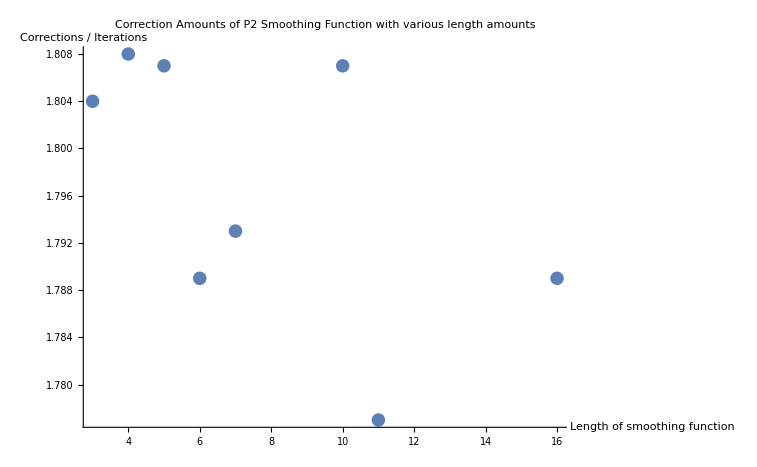

```mathematica
ListPlot[
Table[{RecordedSmoothnessComparisonData[[sm,1,2]],RecordedSmoothnessComparisonData[[sm,3]]/1000.},{sm,2,Length@RecordedSmoothnessComparisonData}],
AxesLabel->{"Length of smoothing function","Corrections / Iterations"},
PlotLabel->"Correction Amounts of P2 Smoothing Function with various length amounts",
ImageSize->Large
]
```